```mathematica
links= Select[Import["http://toti.lindberg.zone/beatles/showall.asp",{"HTML","Hyperlinks"}],StringContainsQ["showsong"]];
```

```mathematica
text = Import[#,{"HTML","Data"}]& /@links;                                    (*Helped by Jesse Friedman*)
```

```mathematica
lyrics = text[[All,2,2]];
```

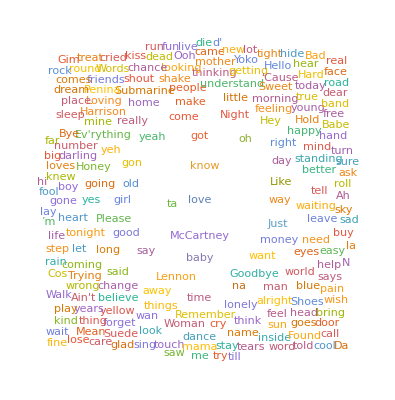

```mathematica
WordCloud[StringRiffle[lyrics], MaxItems->200]
```